```mathematica
<< PenduloComPolia`Importador`;
<< PenduloComPolia`ModeloEDO`;
<< PenduloComPolia`ModeloGeometrico`;
<< PenduloComPolia`CalcularPeriodo`;
<< DerivadaDiscreta`;
<< RotCircle`;
```

```mathematica
(* Todo o processamento será feito sobre essa tomada de vídeo (fizemos 3) *)
```

```mathematica
tomada = 2;
```

## Por que linearizar θ[ϕ] é válido

```mathematica
Module[{ϕ,thetaParaPhi,lista,modeloLinear},
ϕ[θ_]=ArcTan[X[r, L0, θ],Y[r,L0,θ]];
thetaParaPhi[theta_] = ϕ[theta*π/180]/Degree;
lista = Table[{i, thetaParaPhi[i]}, {i,-45,+45,0.1}];
modeloLinear[raio_, comprimento_] := Module[{theta},
LinearModelFit[lista/.{r->raio,L0->comprimento}, theta,theta]
];
Manipulate[
Show[
Plot[thetaParaPhi[theta]/.{r->raio,L0->comprimento}, {theta,-45,45}, AxesLabel->{"θ (°)","ϕ (°)"}, PlotLegends->{"Relação precisa"}],
Plot[modeloLinear[raio,comprimento][theta], {theta, -45,45}, PlotStyle->{Dashed,Red},PlotLegends->{"fit linear"}]
],
{raio,0.078,1},
{comprimento,0.30,1}
]
]
```

```mathematica
S
```

S

## θ[t] teórico e experimental

```mathematica
Manipulate[
Module[{θ},
θ[tempo_]=Quiet[Module[{t},
ReplaceAll[SolucaoNumerica[tomada,{Θ[0]== Listar[tomada, "θ"][[1]], Θ'[0]==omegaInicial},{t, 0, 8}],{t->tempo}]
]];
Show[
Plot[θ[t], {t,0,8}, PlotStyle->Blue, PlotLegends->{"Teórico"}],
ListLinePlot[Listar[tomada,"t","θ"], PlotStyle->Red, PlotLegends->{"Experimental"}],
AxesLabel->{"tempo(s)", "θ(rad)"},
PlotRange->{{0,9},{-0.7,0.7}},
Background->Automatic,
ImageSize->Large
]
],
{omegaInicial, -2,2}
]
```

## Gráfico estático (posições)

```mathematica
omegas= Module[{thetaExp, omegas,t},
For[i=1, i≤ QuantasTomadas[], i=i+1,
thetaExp[i] = Listar[i,"t","θ"];
omegas[i]=DerivadaDiscreta[thetaExp[i]];
];
omegas
];
```

```mathematica
fits = Module[{fit,i,t},
For[i=1,i≤ QuantasTomadas[],i=i+1,
fit[i]=NonlinearModelFit[omegas[i],{a*Cos[b*t+c]}, {{a,3},{b,(2π)/1},c},t, MaxIterations->1000];
];
fit
];
```

```mathematica
θ[tempo_]=Quiet[Module[{t, tempoInicial},
(* Segundo tempo marcado pelo Tracker *)
tempoInicial = omegas[tomada][[1]][[1]];
ReplaceAll[SolucaoNumerica[tomada,{Θ[tempoInicial]== Listar[tomada, "θ"][[2]], Θ'[tempoInicial]== omegas[tomada][[1]][[2]]},{t, 0, 8}],{t->tempo}]
]];
funcaoX[tempo_] = X[Pegar[tomada,"raio da polia"],Pegar[tomada,"comprimento do fio"],theta[t]]/.theta[t]->θ[tempo];
funcaoY[tempo_] = Y[Pegar[tomada,"raio da polia"],Pegar[tomada,"comprimento do fio"],theta[t]]/.theta[t]->θ[tempo];
```

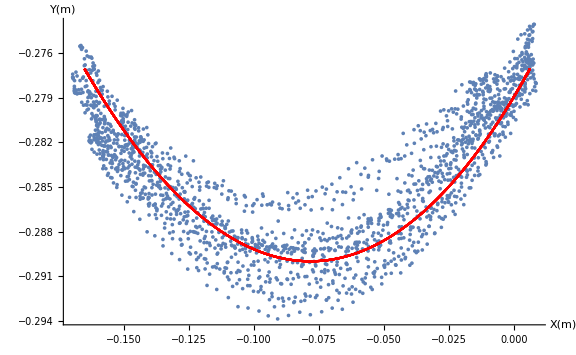

```mathematica
Show[
ListPlot[Listar[tomada,"x","y"]],
ListPlot[Table[{funcaoX[tempo],funcaoY[tempo]},{tempo,0,8,0.001}],PlotStyle->Red],
PlotRange->All,
ImageSize->Large,
AxesLabel->{"X(m)", "Y(m)"}
]
```

## Semiperíodos teóricos e experimentais

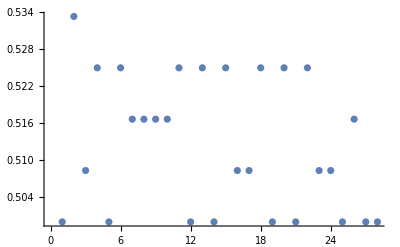

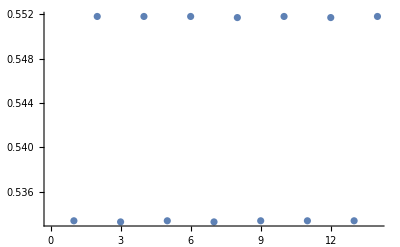

```mathematica
ListPlot[Select[Differences[Map[#[[1]]&,Select[Listar[tomada,"t","θ"],Abs[#[[2]]]<0.02&]]],#>0.05&], PlotLegends->"Semiperíodos experimentais medidos consecutivamente"]
ListPlot[Select[Differences[Map[#[[1]]&,Select[Table[{tempo,θ[tempo]},{tempo,0,8,0.0001}],Abs[#[[2]]]<0.001&]]],#>0.05&], PlotLegends->"Semiperíodos teóricos medidos consecutivamente"]
```

## Energias mecânicas teórica e experimental

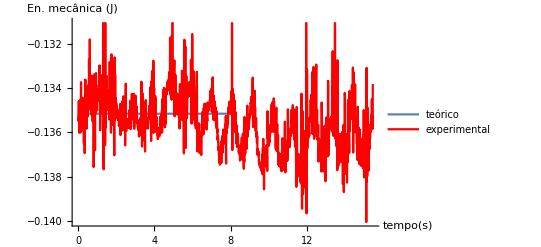

```mathematica
Module[{vxExp, vyExp,vxTeo,vyTeo,yTeo, energiaExp, energiaTeo},
vxExp = DerivadaDiscreta[Listar[tomada,"t","x"]];
vyExp = DerivadaDiscreta[Listar[tomada, "t", "y"]];
energiaExp=
1/2(Map[{#[[1]],Pegar[tomada, "massa oscilante"]*(#[[2]])^2}&,vxExp]+Map[{#[[1]],Pegar[tomada, "massa oscilante"]*(#[[2]])^2}&,vyExp])+Rest[Most[Map[{0,Pegar[tomada,"massa oscilante"]*g*#[[2]]}&,Listar[tomada,"t","y"]]]];
vxTeo=DerivadaDiscreta[Table[{t,funcaoX[t]},{t,0,8,0.001}]];
vyTeo=DerivadaDiscreta[Table[{t,funcaoY[t]},{t,0,8,0.001}]];
yTeo=Rest[Most[Table[{t,funcaoY[t]}, {t,0,8,0.001}]]];
energiaTeo=1/2(Map[{#[[1]],Pegar[tomada, "massa oscilante"]*(#[[2]])^2}&,vxTeo]+Map[{#[[1]],Pegar[tomada, "massa oscilante"]*(#[[2]])^2}&,vyTeo])+Map[{0,Pegar[tomada,"massa oscilante"]*g*#[[2]]}&,yTeo];
Show[
ListLinePlot[energiaTeo, PlotLegends->{"teórico"}],
ListLinePlot[energiaExp, PlotLegends->{"experimental"}, PlotStyle->Red],
AxesLabel->{"tempo(s)", "En. mecânica (J)"},
PlotRange->All
]
]
```

## Simulação

```mathematica
Module[{r, L, centro,tempo, base, pontoContato, posicaoMassa},
r =  Pegar[tomada, "raio da polia"];
L = Pegar[tomada, "comprimento do fio"];
centro = {0,0};
base = 0.04;
pontoContato[tempo_] =centro - {r*Cos[θ[tempo]], r*Sin[θ[tempo]]};
posicaoMassa[tempo_] = {funcaoX[tempo], funcaoY[tempo]};
Animate[
Show[
Graphics[{
Point[centro],
Circle[centro, r],
Line[{pontoContato[t], posicaoMassa[t]}],
Disk[posicaoMassa[t], 0.005]
}],
PlotRange->{{-0.27,0.2},{-0.35,0.1}}
],
{t,0,3*CalcularPeriodoTeo[θ[tempo]]}
]
]
```

## Desenhos

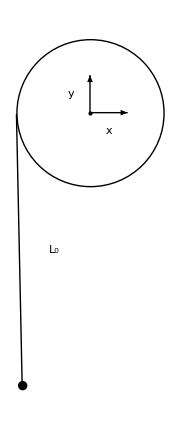

```mathematica
Module[{r, L,tempo, centro, base, pontoContato, posicaoMassa},
r =  Pegar[tomada, "raio da polia"];
L = Pegar[tomada, "comprimento do fio"];
centro = {0,0};
base = 0.04;
tempo = 0.265;
pontoContato =centro - {r*Cos[θ[tempo]], r*Sin[θ[tempo]]};
posicaoMassa = {funcaoX[tempo], funcaoY[tempo]};
Show[
Graphics[{
Point[centro],
Circle[centro, r],
Line[{pontoContato, posicaoMassa}],
Disk[posicaoMassa, 0.005],
(* Dashing[0.03], Line[{pontoContato, pontoContato+{0,-5base}}],
RotCircle[θ[tempo], pontoContato, {0,-base}, {base,0}],
Text["θ(t)",pontoContato+{0,-base}-base/2*{-1,1}],
Text["L(t)", pontoContato+L/2*{Sin[θ[tempo]],-Cos[θ[tempo]]}+{base,0}],
Line[{centro, centro+{r,0}}],
Text["r", centro+r/2{1,0}+{0,base/2}],
Dashing[{}],Thickness[0.02],Arrowheads[Large],Red,Arrow[{posicaoMassa,(pontoContato+posicaoMassa)/2}],
Arrow[{posicaoMassa, posicaoMassa-{0,0.1}}],
Black,Text["T(t)", posicaoMassa+{0,base}],
Text["mg", posicaoMassa-{base,base}], *)
Text["L_0", pontoContato+{base,-L/2}],
Arrow[{centro, centro+{base,0} }],
Arrow[{centro,centro+{0,base}}],
Text["x",centro+base/2{1,-1}],
Text["y",centro+base/2{-1,1}]
}],
ImageSize->Small
]
]
```